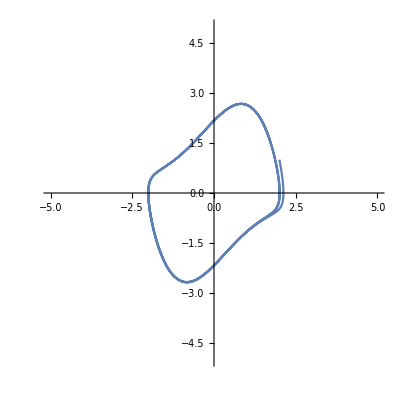

```mathematica
mu = 1;
eqns = {x'[t] == y[t], y'[t] == mu*(1 - x[t]^2)*y[t] - x[t]};
ic = {x[0] == 2, y[0] == 1};
sol = NDSolve[{eqns, ic}, {x, y}, {t, 0, 50},Method->"ExplicitRungeKutta"];
ParametricPlot[Evaluate[{x[t], y[t]} /. sol], {t, 0, 20}, PlotRange -> {{-5, 5}, {-5, 5}}]
```

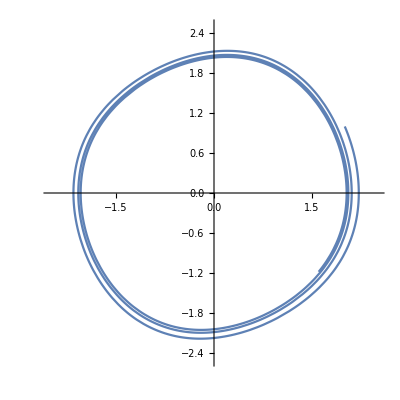

```mathematica
mu = 0.1;
eqns = {x'[t] == y[t], y'[t] == mu*(1 - x[t]^2)*y[t] - x[t]};
ic = {x[0] == 2, y[0] == 1};
sol = NDSolve[{eqns, ic}, {x, y}, {t, 0, 50},Method->"ExplicitRungeKutta"];
ParametricPlot[Evaluate[{x[t], y[t]} /. sol], {t, 0, 20}, PlotRange -> {{-2.5, 2.5}, {-2.5, 2.5}}]
```